# Molecular Dynamics Notes

## Enter subtitle here

Enter subsubtitle here

Phil Shea

Enter department here

```mathematica
DateString[]
```

Mon 6 Oct 2025 11:45:14

Enter date here

## General Parameters

### Layout of the Initial Positions

#### Area of Veroni Cell

The initial position is based on a hexagonal grid oriented to the box sides.  Let b_x and b_y be half the sides of the box; the box has corners {{-b_x,-b_y},{b_x,-b_y}, {b_x,b_y},{-b_x, b_y}}   The box area is then the product of these, and the density is ρ = N / (4 b_xb_y), where N is the number of particles in the system.  In the figure below, Q_1 is the center particle, and positions H, I, J, K, L, and M are the adjacent particles.  Let the hexagonal lattice have particle spacing a (Q_1 - J below). The Veroni cell around each particle consists of twelve 30-60-90 degree right triangles with sides a/2 (Q_1-S_1 in the figure below), a/(2√3) (S_1-E), and hypotenuse a/√3 (Q_1 - E; the ‘ marks are from the GeoGebra drawing program indicating how many time the point was used in the drawing).

-Graphics-

See Fukshansky 2011

The hypotenuse (Q_1 - E) is given by the following:

```mathematica
Solve[a/2 ==r Cos[30 Degree],r]
```

{{r→a/(√3)}}

The short side is therefore

```mathematica
(a/√3)Sin[30 Degree]
```

a/(2 √3)

The area occupied by one particle is then:

```mathematica
area=12(a/2)(a/(2 √3))(1/2)
```

(√3 a^2)/2

To achieve a specified density, solve the following:

```mathematica
Solve[(√3 a^2)/2==1/ρ,a]
```

{{a→-(√2)/(3^(1/4) √ρ)},{a→(√2)/(3^(1/4) √ρ)}}

The paper from 1980 used a density of ρ = 1/π and an a a bit bigger than 1.9σ

```mathematica
α79=Simplify[(√2)/(3^(1/4) √(1/π))]
```

(√(2 π))/3^(1/4)

```mathematica
a79=N[α79]
```

1.90463

The box dimensions can be decided for a desired density.  ρ = N/(4 b_x b_y) = N/(2√3b_x^2) (where b_y = √3 b_x/2

```mathematica
ClearAll[Bx];
Bx::usage="Bx[K,ρ] will create the x dimension for an array of K particles at density ρ. 
K should be an integer.";
Bx[K_,ρ_]:=√(K/(2 √3 ρ))
```

```mathematica
bx256=Bx[256, 1/π]
```

(8 √(2 π))/3^(1/4)

```mathematica
N[%]
```

15.237

```mathematica
by256=√3 bx256/2
```

4 3^(1/4) √(2 π)

```mathematica
N[%]
```

13.1956

The particle positions then will be Nr rows each having Nc particles (this assumes N is composite).  The following function will place a row of n particles spaced by a starting at position {x, y}:

```mathematica
ClearAll[ placeR];
placeR::usage="placeR[n, a, x, y] will place a row of n particles spaced by a starting 
at position {x, y}";
placeR[n_, a_, x_, y_]:=Table[{x + i a, y},{i,0,n-1}]
```

Here is an example:

```mathematica
placeR[4, .3, .3/4, 0]
```

{{0.075,0},{0.375,0},{0.675,0},{0.975,0}}

This function will fill a rectangle, and the two parameter version will make the standard rectangle.

```mathematica
ClearAll[ fill];
fill::usage="fill[ Bx, By, K] will place K particles in a hexagonal grid in a rectangle of 
size 2Bx x 2By.  If K is not a perfect square such that all the rows have the same number of 
particles, it may be adjusted to fit the dimensions. Returns a seven element association 
{\"ρ\", \"a\", \"Nc\", \"Nr\", \"Bx\", \"By\", \"pn\"} repectivley the density, particle spacing, 
number of columns and rows, and the input box parameters (note the quotes are required). 
\"pn\" is a nested list of {x, y} coordinates of the K particle positions
fill[...]⟦\"pn\"⟧ is pnts = {{{x11,y11},[x12,y12}...{x1Nc,y1Nc}},
{{x21,y21},...},...{{xNr1,yNr1},...,{xNrNc,yNrNc}}}.  Thus, point one's coordinates are best
accessed via Flatten[ pnts,1]⟦1⟧).

fill[ Bx, K] (the two parameter version) will set By to the default of (√3/2)Bx.";
fill[Bx_, By_, K_]:= Module[{ρ=K/(4Bx By),a,Nc,Nr,c},
	a=√(2/(ρ √3)); c=√3/2; Nc=Round[2 Bx/a]; Nr=Round[K/Nc];
	Association[{"ρ"->ρ, "a"->a, "Nr"->Nr, "Nc"->Nc, "Bx"->Bx, "By"->By,
		"pn"->Table[placeR[Nc, a, (a/4)(1+2Mod[i,2])-Bx,a c(i+1/2)-By],{i,0,Nr-1}]}]];
fill[Bx_, K_]:= fill[Bx, (√3/2)Bx,K]
```

```mathematica
t=Association[{ρ->1/π,a->10, "p1"->p1}]
```

<|ρ→1/π,a→10,p1→p1|>

```mathematica
{t[ρ],t["p1"]}
```

{1/π,p1}

Here is an example of 10 particles:

```mathematica
pnts10=fill[10,25]
```

<|ρ→1/(8 √3),a→4,Nr→5,Nc→5,Bx→10,By→5 √3,pn→{{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3}},{{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3}},{{-9,0},{-5,0},{-1,0},{3,0},{7,0}},{{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3}},{{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}}|>

```mathematica
pnts10⟦{"ρ","a"}⟧
```

<|ρ→1/(8 √3),a→4|>

```mathematica
Flatten[pnts10⟦"pn"⟧,1]
```

{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3},{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3},{-9,0},{-5,0},{-1,0},{3,0},{7,0},{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3},{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}

```mathematica
%⟦1⟧
```

{-9,-4 √3}

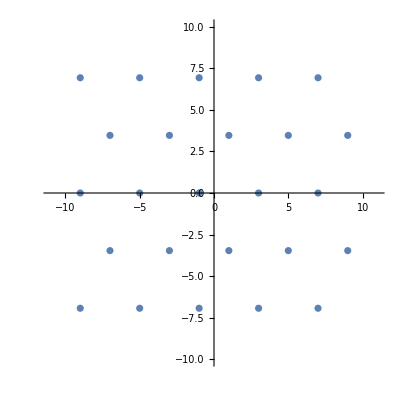

```mathematica
ListPlot[Flatten[pnts10⟦"pn"⟧,1],AspectRatio->1, PlotRange-> {{-11,11},{-10,10}},GridLines->{{-10,10},{-10√3/2,10√3/2}}]
```

A function to plot the points returned by fill[] will be useful:

```mathematica
ClearAll[plotPnts];
 plotPnts[pnts_]:=Module[{Bx=pnts⟦"Bx"⟧, By=pnts⟦"By"⟧, box},box={{-Bx, Bx}, {-By, By}};
 ListPlot[Flatten[pnts⟦"pn"⟧, 1], AspectRatio->1, PlotRange->1.1box, GridLines->box]]
```

The returned values of the first element are the density, the spacing, number of rows and columns, and Bx & By.

```mathematica
pnts256=fill[Bx[256, 1/π],256];
pnts256⟦{"ρ","a","Bx","By"}⟧
```

<|ρ→1/π,a→(√(2 π))/3^(1/4),Bx→(8 √(2 π))/3^(1/4),By→4 3^(1/4) √(2 π)|>

```mathematica
3.5/pnts256⟦"a"⟧
```

1.83763

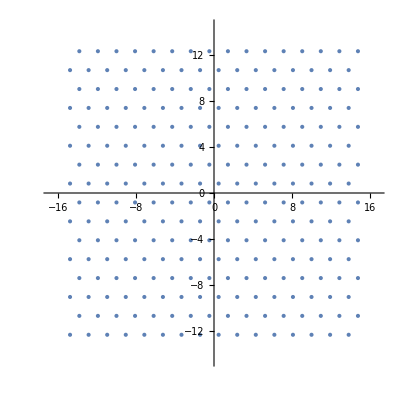

```mathematica
p256=plotPnts[pnts256]
```

Here is a 256 particle array, with a focus on particle 189.  The red circle is the skin range of 3.5, and the green circle is the correlation range (the shell) of 5.  The magenta circled particle is the next nearest particle on the row, and the blue circled particle is the second next nearest particle, just inside the skin.

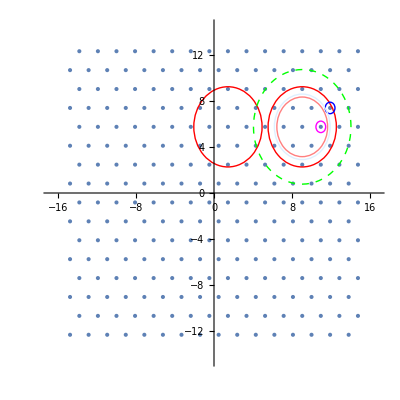

```mathematica
pnts256arr = Flatten[pnts256⟦"pn"⟧,1];
p1=pnts256arr⟦189⟧; (* Focal point *)
p2=pnts256arr⟦190⟧; (* Next point on row *)
p3=pnts256arr⟦207⟧; (* next nearest neighbor *)
p4=pnts256arr⟦189-4⟧; (* secondary shell center *)
Rskin = 3.5; Rshell = 5;
Show[p256,Graphics[{Red,Circle[p1,Rskin]}],Graphics[{Red,Circle[p4,Rskin]}],Graphics[ {Magenta,Circle[p2,0.5]}],Graphics[{Green, Dashed,Circle[p1, Rshell]}],Graphics[ {Blue, Circle[p3,0.5]}],Graphics[{Pink, Circle[ p1, (1 + √3)* pnts256⟦"a"⟧/2]}],Graphics[{LightBlue, Circle[ p1, 3* pnts256⟦"a"⟧/2]}]]
```

The red circles above show that they do not overlap. They could be set to 2a so that they would touch.  There would be a few more interacting particles then, and, at initialization, six particles would sit on the skin.

```mathematica
Simplify[p2-p1]
```

{(√(2 π))/3^(1/4),0}

```mathematica
Simplify[EuclideanDistance[p1,p2]]
```

(√(2 π))/3^(1/4)

```mathematica
%==a79
```

True

```mathematica
nnnd=Simplify[EuclideanDistance[p1,p3]/α79] (*next nearest neighbor distance in 1/π density interparticle distance units*)
```

√3

```mathematica
N[%]
```

1.73205

The third nearest neighbor is 2a, which is just outside the skin.

```mathematica
tnnnd=2α79
```

(2 √(2 π))/3^(1/4)

```mathematica
N[%]
```

3.80925

Particle 208 (and all the others near the green circle) lies very near the shell at 5.

```mathematica
N[pnts256arr⟦208⟧]
```

{13.8085,7.42254}

```mathematica
fnnd=Simplify[EuclideanDistance[p1,pnts256arr⟦208⟧]]
```

(√(14 π))/3^(1/4)

```mathematica
N[%]
```

5.03917

Just a hair past the shell.

### Angular Momentum

When applying random velocities to the particles, the velocities in the x and y directions will each be drawn from a zero-mean Gaussian distribution. The sum of velocities in the x and y direction will therefore also be zero-mean, but will have a substantial variance: for N particles, the variance will be Nσ^2.  Therefore, after initialization, we need to measure the momentum in the x and y directions and subtract that average per-particle momentum from each particle.

The same is true for angular momentum. It just won’t do for the whole system to be rotating, even a little. It is easy to measure the angular momentum. For a particle with a vector position x and vector velocity v, and particle mass m, the angular momentum about the origin is L = x × m v. In two dimensions,

```mathematica
A ={ax,ay,az};V ={vx,vy,vz};L=Cross[A,V]
```

{-az vy+ay vz,az vx-ax vz,-ay vx+ax vy}

This is very simple when the z components are zero.

```mathematica
L/.{az-> 0, vz->0}
```

{0,0,-ay vx+ax vy}

The total angular momentum is then L =∑_(i=1)^N x_i×v_i, where we assume m = 1. This can also be considered as an average rotation rate Ω, and the angular momentum can then also be expressed as L =∑_(i=1)^N r_iω =ω∑_(i=1)^N r_i, where r_i is the radial component of the particle i in cylindrical coordinates (that is, its distance from the origin). If S = ∑_(i=1)^N r_i (sort of a moment of inertia in scaled units), then the average rotation rate is given by ω = L/S, and therefore the ith particle’s share of the rotation is l_i = ω r_i.

We can calculate ω, and then say that l = ax vy - ay vx. This is insufficient to calculate a velocity vector, but the velocity vector is orthogonal to the particle vector, so their dot product will be zero.

```mathematica
Solve[l==ax vy-ay vx&&ax vx+ay vy==0,{vx,vy}]
```

{{vx→-(ay l)/(ax^2+ay^2),vy→(ax l)/(ax^2+ay^2)}}

#### Numerical Assessments

The value of S (scaled moment of inertia) is somewhat large:

```mathematica
S=Apply[Plus,Map[Norm,N[pnts256arr]]]
```

2786.81

One measurement of L was around 58. ω is then

```mathematica
58/S
```

0.0208123

```mathematica
%/(2π)
```

0.00331239

```mathematica
1/%
```

301.897

So, with that high value of L, it would take a time of almost 302, or 30,000 time steps to make a full rotation. However, only a small rotation would be a problem with the crystal interfaces at the boundaries.

The maximum range is a bit over 19:

```mathematica
Max[Map[Norm,N[pnts256arr]]]
```

19.2593

This means that even the farthest particles will only get less than 1% of the total angular momentum, but this is still more than twice what they would get if the momentum was evenly divided among the 256 particles.

```mathematica
S/%
```

144.699

### Problems with Large Number of Particles

While 256 particles was relatively straight forward, there are some issues as we try to scale to one million particles.

#### Correlation Array Length

The correlation array records all inter-particle interactions once each.  That is, if particle one interacts with particle two but not particle three, and particle two interacts with one and three, particle two’s list only includes particle three.  Interactions are limited by the the shell radius R_shell.  Since the overall density is fixed, the average number of interactions per particle is simply π ρ R_shell^2, where ρ is the density. For the 1980 system, R_shell=5 and ρ=1/π, so this number is simply 25.  With 256 particles, and each interaction only counting once, there should be no more than 255 · 25 / 2 = 3,187.5.  In fact, in 17,472 executions (of varying number of steps up to 50,000), the maximum we have observed is 3,115.  This was determined through the steps below.

```mathematica
home:$ cd ~/MD/Data/1980
~/MD/Data/1980$ grep "Max number of interactions:" *.txt > MNI.txt
~/MD/Data/1980$ R # Start R
R version 4.5.1 (2025-06-13) -- "Great Square Root"
Copyright (C) 2025 The R Foundation for Statistical Computing
Platform: x86_64-pc-linux-gnu

> td <- "/media/phil/Original/Users/phils/Documents/DSP/MD/Data/1980"
> x <- read.delim( paste( td, "MNI.txt", sep = "/"), ":", header=FALSE)
> max(x$V3)
[1] 3115
```

The current minimum the program allows (as of August 2025) is double this: N π ρ R_shell^2, where N is the number of particles (6,400) in the current system), and the executions have been using 9,728 (N * round(1.5 * pi * density *Rshell^2)).  So, as we get to 2^20 (one million) particles, we need to have a tighter bound, and  N π ρ R_shell^2/2 would occupy about 105MB of memory (assuming 4 bytes per integer), large, but doable. A 10% margin should be added as we wouldn’t want a calculation to fail after hours of work just because this limit was too tight.

#### Correlation Algorithm

Currently, the simulation stops every 50 steps and calculates the distance between all particle pairs to create the list of those within each particle’s shell.  So particle one looks at the the distance to the other 255 particles. Particle two looks at 254, and so on.

```mathematica
Simplify[ Sum[ i, {i, 1, N-1}]]
```

1/2 (-1+N) N

So this dependence on (N^2-N)/2 can get big.

```mathematica
paircnt[N_]:=(N^2-N)/2;
Table[ {i,2^i,paircnt[2^i]}, {i,8,20,2}]
```

{{8,256,32640},{10,1024,523776},{12,4096,8386560},{14,16384,134209536},{16,65536,2147450880},{18,262144,34359607296},{20,1048576,549755289600}}

We might be able to correlate 16K particles in a reasonable amount of time (134M correlations), but the million particle system requires over a half trillion comparisons, each of which requiring two squaring operations. There are a few references of faster ways (see Kim2025, Awhile2012, or Groß2019) that include divide and conquer, spatial hashing, and various tree based algorithms. Groß2019 appears closest to the amount of effort I’m willing to expend in this regard. The idea is to sort the particles by both x and y coordinates, and find those within the square grid defined by the particles position {x_i, y_i}±R_shell.  This is bigger than the circle currently used, as its size is 4R_shell^2 vs. πR_shell^2. At our density of 1/π, that is

```mathematica
N[(4 Rshell^2 - π Rshell^2)/π]
```

6.83099

almost seven extra particles.  The procedure requires two sorts, a search of the sorted list for the box limits in both lists, and then building the list of of particles in the box. We need to keep the particle interaction list in more-or-less ascending order too.  That is, particle i’s list of interacting particles should only contain particle numbers greater then i. The particles within i’s list need not be in any order.

Let’s look at the ten particle system created above as an example.

```mathematica
pnts10
```

<|ρ→1/(8 √3),a→4,Nr→5,Nc→5,Bx→10,By→5 √3,pn→{{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3}},{{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3}},{{-9,0},{-5,0},{-1,0},{3,0},{7,0}},{{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3}},{{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}}|>

Here are the points.

```mathematica
p10=Flatten[pnts10⟦"pn"⟧,1]
```

{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3},{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3},{-9,0},{-5,0},{-1,0},{3,0},{7,0},{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3},{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}

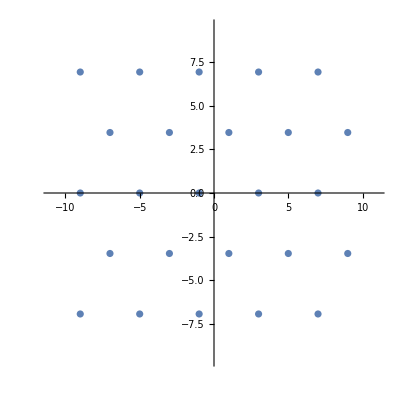

```mathematica
plotPnts[pnts10]
```

```mathematica
TableForm[p10]
```

-9 | -4 √3
-5 | -4 √3
-1 | -4 √3
3 | -4 √3
7 | -4 √3
-7 | -2 √3
-3 | -2 √3
1 | -2 √3
5 | -2 √3
9 | -2 √3
-9 | 0
-5 | 0
-1 | 0
3 | 0
7 | 0
-7 | 2 √3
-3 | 2 √3
1 | 2 √3
5 | 2 √3
9 | 2 √3
-9 | 4 √3
-5 | 4 √3
-1 | 4 √3
3 | 4 √3
7 | 4 √3

Just the x coordinates:

```mathematica
TableForm[xlist=p10⟦All,1⟧]
```

-9
-5
-1
3
7
-7
-3
1
5
9
-9
-5
-1
3
7
-7
-3
1
5
9
-9
-5
-1
3
7

a list showing their order.

```mathematica
xs=Ordering[xlist]
```

{1,11,21,6,16,2,12,22,7,17,3,13,23,8,18,4,14,24,9,19,5,15,25,10,20}

And here is the ordered list:

```mathematica
TableForm[p10⟦xs⟧]
```

-9 | -4 √3
-9 | 0
-9 | 4 √3
-7 | -2 √3
-7 | 2 √3
-5 | -4 √3
-5 | 0
-5 | 4 √3
-3 | -2 √3
-3 | 2 √3
-1 | -4 √3
-1 | 0
-1 | 4 √3
1 | -2 √3
1 | 2 √3
3 | -4 √3
3 | 0
3 | 4 √3
5 | -2 √3
5 | 2 √3
7 | -4 √3
7 | 0
7 | 4 √3
9 | -2 √3
9 | 2 √3

When we cut a swath in the x-axis of height R_shell, it will occupy an area of 2B_xR_shell.  For our 1M point example,

```mathematica
Bx1M=Bx[2^20,1/π]
```

(512 √(2 π))/3^(1/4)

```mathematica
N[%]
```

975.168

The number of particles in a swath ±R_shell wide is then:

```mathematica
N[2Bx1M Rshell/π]
```

3104.06

The number of points

```mathematica
By1M=(√3/2)Bx1M
```

256 3^(1/4) √(2 π)

```mathematica
N[%]
```

844.521

```mathematica
N[2By1M Rshell/π]
```

2688.19

We need to build the periodic boundary conditions into these results, but we’ll save that for the Julia code.  Let’s look at a particle near the middle of the array. When creating the million point system, we wrap N[] around Bx[] to cause each value to be turned into a real number, otherwise the particle list is a very long symbolic expression.

```mathematica
pnts1M=fill[N[Bx[2^20, 1/π]],2^20];
pnts1M⟦"pn"⟧⟦1⟧;
p1M=Flatten[pnts1M⟦"pn"⟧,1];
po=p1M⟦2^19-512⟧
```

{-0.476156,-0.824727}

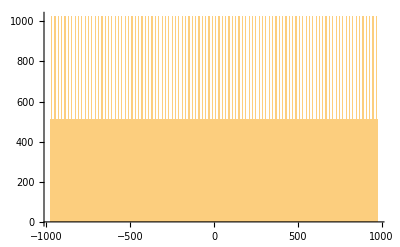

```mathematica
Histogram[p1M⟦All,1⟧,2000]
```

Those tiny peaks are the columns in which the particles line up.

```mathematica
xl1M =Ordering[p1M⟦All,1⟧];yl1M=Ordering[p1M⟦All,2⟧];
```

That appeared pretty fast. Finding a particle should be easy, as it’s position in the list should be close to

```mathematica
coor[x_,side_,K_]:=Round[(x+side)/(2side/K)]
```

```mathematica
pon=coor[po⟦1⟧,Bx1M,2^20]
```

524032

That looks about right.

```mathematica
xl1M⟦pon⟧
```

523776

```mathematica
p1M⟦%⟧
```

{-0.476156,-0.824727}

So that was exact (these particles are in their home positions).  Now let’s find the indices of particles in the x axis shell

```mathematica
po⟦1⟧+{-Rshell,Rshell}
```

{-5.47616,4.52384}

We want a list of particle numbers whose x-coordinates exist between these values. Since we already have a sorted list, wee can use it.

```mathematica
pox=coor[%,Bx1M,2^20]
```

{521344,526720}

The difference between these will show us the number of elements.

```mathematica
pox⟦2⟧-pox⟦1⟧
```

5376

That’s more than we expected.

```mathematica
TableForm[p1M⟦xl1M⟦pox⟦1⟧+{-5,-4,-3,-2,-1,-0,1,2,3,4,5}⟧⟧]
```

-5.23772 | -441.229
-5.23772 | -437.93
-5.23772 | -434.631
-5.23772 | -431.332
-5.23772 | -428.033
-5.23772 | -424.734
-5.23772 | -421.436
-5.23772 | -418.137
-5.23772 | -414.838
-5.23772 | -411.539
-5.23772 | -408.24

So here is the first challenge with the technique.  We may not have found the correct limits as many elements are repeated due to particles being in home position.  We need to search from there and find the correct starting point. Again, we’ll wait until we implement in Julia for this fiddly code, and we’ll simply dither the positions a bit.

```mathematica
0.01RandomVariate[NormalDistribution[0,1],{10,2}]
```

{{0.00946029,-0.000527877},{0.000467987,-0.00796553},{-0.0132054,0.00335214},{-0.0141177,-0.00480895},{0.00174142,-0.010718},{-0.0135508,0.00627208},{-0.00582092,0.0066283},{-0.013254,-0.0244211},{-0.00301322,0.00996121},{0.00831837,0.00313206}}

```mathematica
p1Md=p1M+ 0.01RandomVariate[NormalDistribution[0,1],{Length[p1M],2}];
xl1Md =Ordering[p1Md⟦All,1⟧];yl1Md=Ordering[p1Md⟦All,2⟧];
```

The pox list doesn’t need to change, as it was simply a guess into where in the array the values would occur.

```mathematica
TableForm[p1Md⟦xl1Md⟦pox⟦1⟧+{-5,-4,-3,-2,-1,-0,1,2,3,4,5}⟧⟧]
```

-5.2445 | -325.763
-5.24439 | -698.533
-5.24433 | 63.5168
-5.24422 | -124.533
-5.24404 | 736.461
-5.24401 | 406.601
-5.24394 | 70.1042
-5.24393 | 578.143
-5.24375 | 686.991
-5.24374 | -612.763
-5.24369 | 17.3281

```mathematica
Clear[p1M,pnts1M,xl1M,yl1M,xl1Md,yl1Md, p1Md,p1M]
```

```mathematica
p1Mr=RandomReal[{-Bx1M,Bx1M},{2^20,2}];
xl1Mr =Ordering[p1Mr⟦All,1⟧];yl1Mr=Ordering[p1Mr⟦All,2⟧];
```

```mathematica
TableForm[p1Mr⟦xl1Mr⟦pox⟦1⟧+{-5,-4,-3,-2,-1,-0,1,2,3,4,5}⟧⟧]
```

-5.48515 | -327.346
-5.4828 | 751.951
-5.48268 | -446.276
-5.47873 | 774.901
-5.47471 | -61.4106
-5.47397 | 426.639
-5.47189 | 818.123
-5.47021 | 72.5395
-5.46691 | 87.493
-5.46671 | 416.66
-5.46134 | 504.021

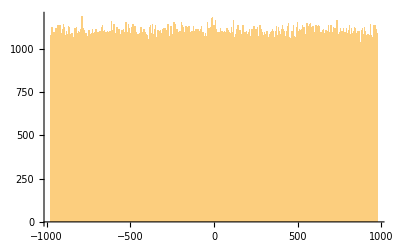

```mathematica
Histogram[p1Mr⟦All,1⟧,1000]
```

```mathematica
po=p1Mr⟦xl1Mr⟦2^19-512⟧⟧
```

{-0.988239,400.622}

```mathematica
po⟦1⟧
```

-0.988239

```mathematica
po⟦1⟧+{-Rshell,Rshell}
```

{-5.98824,4.01176}

We want a list of particle numbers whose x-coordinates exist between these values. Since we already have a sorted list, wee can use it.

```mathematica
pox=coor[%,Bx1M,2^20]
```

{521068,526445}

The difference between these will show us the number of elements.

```mathematica
pox⟦2⟧-pox⟦1⟧
```

5377

That’s about half of what we expected.

```mathematica
TableForm[p1Mr⟦xl1Mr⟦pox⟦1⟧+{-5,-4,-3,-2,-1,-0,1,2,3,4,5}⟧⟧]
```

-5.99502 | -859.253
-5.9943 | 8.99668
-5.99399 | 925.448
-5.99399 | 181.561
-5.99267 | 532.593
-5.992 | 398.381
-5.98397 | 371.049
-5.98265 | -974.073
-5.98262 | -49.1208
-5.98226 | 736.418
-5.98215 | 495.344

Below is a plot of the x-coordinates as a sorted list.

```mathematica
ListPlot[p1Mr⟦xl1Mr,1⟧]
```

-Graphics-

Timings of the current algorithm.  The log-log plot makes it look like it is linear.

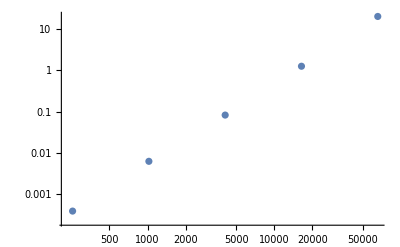

```mathematica
origtime={{256,0.00038},{1024,0.006171},{4096,0.0823},{16384,1.268},{65536,20.61}};
ListLogLogPlot[origtime]
```

This is the time per particle.

```mathematica
tpp=Apply[#2/#1&,origtime,{1}]
```

{1.48438×10^-6,6.02637×10^-6,0.0000200928,0.0000773926,0.000314484}

This is increasing on a per particle basis.

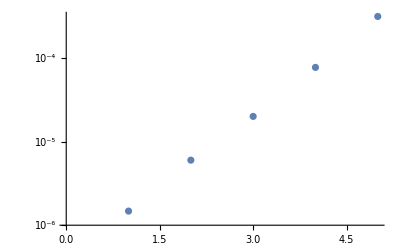

```mathematica
ListLogPlot[tpp]
```

We can quickly eliminate particles whose distance is greater than the shell (or the skin for that matter) in  either the x or y direction, and can include those whose x and y distance are both less than the 1/√2 of the shell distance.

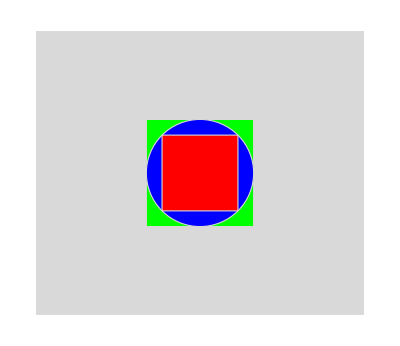

```mathematica
Graphics[{EdgeForm[Thick],LightGray,Rectangle[{-bx256, -by256},{bx256, by256}],Green, Rectangle[{-Rshell,-Rshell},{Rshell,Rshell}],Blue,Disk[{0,0},Rshell], Red,Rectangle[{-Rshell, -Rshell}/√2,{Rshell,Rshell}/√2]}]
```

The number of points in these limits at a distance of R is 4R^2/ρ for the outer square, πR^2/ρ for the circle.  The inner square’s diagonal is 2R, so  4R^2=2 x^2 and x=√2 R, and the area is 2R^2, or half the area of the green square.  If this seems odd, not that the green wide strip at the bottom is 2R wide, and (1-1/√2)R tall, and there are two, and the two vertical strips are as wide as the latter were tall, and √2 R tall.  Their area is:

```mathematica
Simplify[2(2r)(1-1/√2)r+2r(1-1/√2)√2 r]
```

2 r^2

So there is the other half.  For our current density, the average number of particles in these areas are then:

```mathematica
N[{{Green, 4 Rshell^2/π},{Blue,Rshell^2},{Red,2 Rshell^2/π}}]
```

{{RGBColor[0., 1., 0.],31.831},{RGBColor[0., 0., 1.],25.},{RGBColor[1., 0., 0.],15.9155}}

Current BaselineSpeedtest results (8/25/25):
16.915548 seconds (20.15 M allocations: 1.577 GiB, 3.27% gc time, 170 lock conflicts)

As a reminder, the times for the original algorithm are below.

```mathematica
TableForm[origtime]
```

256 | 0.00038
1024 | 0.006171
4096 | 0.0823
16384 | 1.268
65536 | 20.61

Using the above comparison based testing, the 65K run was reduced to 5.1s, a factor of four.  While hopeful, 2^18 particle (262,144) CorrShell!() took 80.8s (per particle about four times longer than 2^16).

```mathematica
origtime = Append[ origtime, {2^18, 262.144}]
```

{{256,0.00038},{1024,0.006171},{4096,0.0823},{16384,1.268},{65536,20.61},{262144,262.144}}

With this now in the mainline CorrShell!() code, the BaselineSpeed was a bit faster:

13.940024 seconds (20.15 M allocations: 1.577 GiB, 3.52% gc time, 199 lock conflicts)

After adding inrangeq() to the GetForce!() function, we got:

13.441450 seconds (20.15 M allocations: 1.577 GiB, 3.65% gc time, 193 lock conflicts)

The first running of FastCorr!() based on sorting and searching was not a success:

julia> SpeedTest.FastCorrSpeedTest1(2^18,1/pi)
⋮
577.738706 seconds (8.14 M allocations: 664.980 GiB, 4.34% gc time)
784385

That was over seven times longer, and a lot of allocations.  There doesn’t seem to be an easy way of getting Julia to pre-allocate sets, so I’m abandoning this approach.

#### Second Attempt

The next approach will be to divide the field into overlapping boxes of sides R_shell and spaced byR_shell. We will want at least three boxes in each dimension so b_x and b_y must both be greater thanR_shell/2and the box sides must be greater thanR_shell.  Thus the boxes will extend beyond the field. The minimum number of boxes in each direction can be found by solving the following:

```mathematica
Reduce[Rs>0&& l≥Rs&&2b>Rs&&(2n+1) l==2b &&n≥3, {n,l}]
```

b>0&&((0<Rs<(2 b)/7&&3≤n≤(2 b-Rs)/(2 Rs))||(Rs==(2 b)/7&&n==3))&&l==(2 b)/(1+2 n)

```mathematica
Clear[Kx,Ky,Lx,Ly];
N[{bx256, by256,Rshell,Kx = Floor[(bx256/Rshell) -(1/2)], Ky =  Floor[by256/Rshell-1/2], Lx =N[2bx256/(1+2Kx)],Ly =N[2by256/(1+2Ky)]}]
```

{15.237,13.1956,5.,2.,2.,6.0948,5.27825}

```mathematica
N[2bx256/Rshell]
```

6.0948

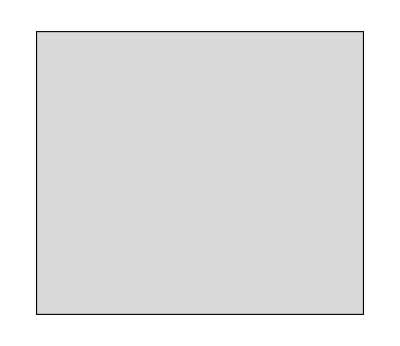

```mathematica
field256=Graphics[{EdgeForm[{GrayLevel[0], Thickness[Large]}], GrayLevel[0.85], 
  Rectangle[{-bx256, -by256}, 
   {bx256, by256}]}]
```

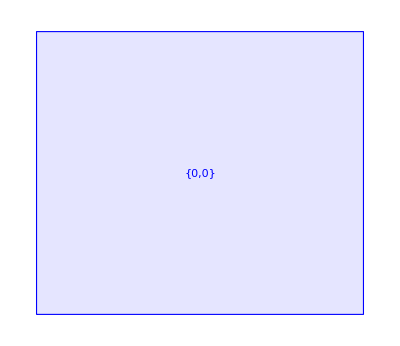

```mathematica
shellbox256=Graphics[ {EdgeForm[Thickness[Tiny]], Blue, FaceForm[Opacity[0.1]], 
  Rectangle[(1/2){-Lx, -Ly}, 
   (1/2){Lx, Ly}], Text[Style[{0,0},Tiny], {0,0}]}]
```

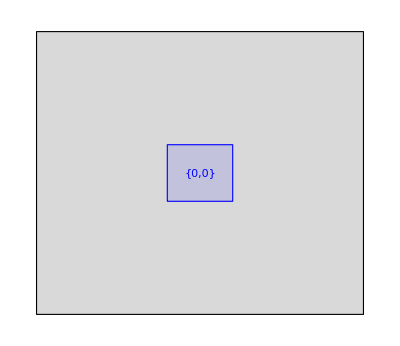

```mathematica
Show[field256,shellbox256]
```

We need a function that will plot a rectangle of a particular size with its center at a particular place and its coordinate printed at its center.

```mathematica
ClearAll[plotrect];
plotrect::usage="plotrect[{xc,yc},{lx,ly},txt] plots a rectangle centered on {xc,yc} with 
sides {lx,ly} and labeled in the center with txt."
plotrect[{xc_,yc_},{lsx_,lsy_}, txt_]:={EdgeForm[Thickness[Tiny]],Blue, FaceForm[Opacity[0.1]], 
  Rectangle[-1{lsx/2,lsy/2}+{xc,yc},{lsx/2,lsy/2}+{xc,yc}], Text[Style[txt,Tiny], {xc,yc}]}
```

plotrect[{xc,yc},{lx,ly},txt] plots a rectangle centered on {xc,yc} with 
sides {lx,ly} and labeled in the center with txt.

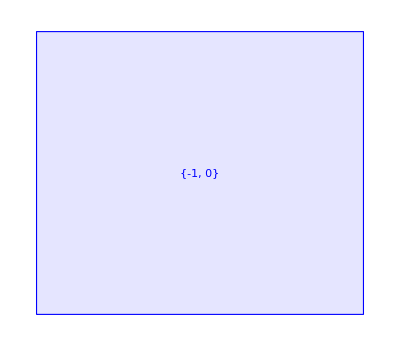

```mathematica
p3=Graphics[plotrect[{-Lx,0}, {Lx,Ly},ToString[{-1,0}]]]
```

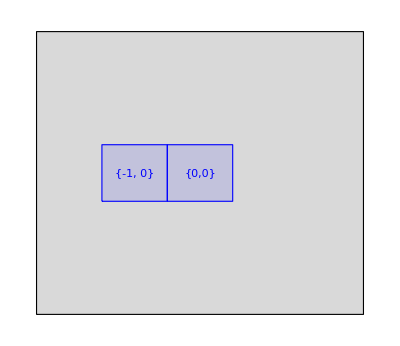

```mathematica
Show[field256, shellbox256, p3]
```

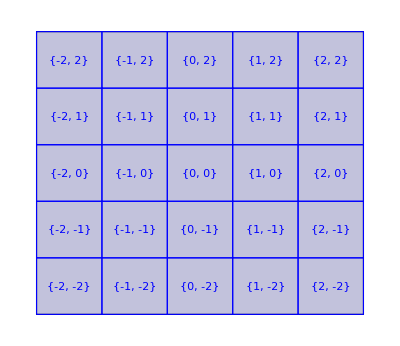

```mathematica
Show[field256,Table[Graphics[plotrect[{i Lx,j Ly},{Lx,Ly},TextString[{i,j}]]],{i,-Kx, Kx},{j,-Ky, Ky}]]
```

This creates an 5x5 array.

Now the box size is ({x,y}):

```mathematica
N[2{bx256/(2Kx+1),by256/(2Ky+1)}]
```

{6.0948,5.27825}

Which would have the following average number of particles in it.

```mathematica
Apply[Times,%]*(1/π)
```

10.24

And nine such boxes would have the following number of particles (on average):

```mathematica
9*%
```

92.16

First successful test for 65,536 particles was 0.049s, 2^18 took only 0.189s, and 2^20 was only 0.755s. 256 particles took 314μs

```mathematica
FastCorr={{256, 0.000314},{1024, 0.000917},{4096, 0.003485},{16384, 0.013133},{2^16, 0.048505},{2^18,0.189100},{2^20, 0.754521}}
```

{{256,0.000314},{1024,0.000917},{4096,0.003485},{16384,0.013133},{65536,0.048505},{262144,0.1891},{1048576,0.754521}}

julia> SpeedTest.FastCorrSpeedTest1(2^20,1/pi,shellM=25)
  0.754521 seconds
12178618

As a reminder, the original algorithm took 577s (over 9.5 minutes) for 2^18.

We can compare the original times with those of FastCorr! via the following.  This will divide each pair of numbers.

```mathematica
MapThread[#1/#2&,{origtime, Drop[FastCorr, -1]},2]
```

{{1,1.21019},{1,6.72955},{1,23.6155},{1,96.5507},{1,424.905},{1,1386.27}}

Even the 256 particle system is faster with FastCorr!.  We did not measure the original algorithm for 2^20 particles, but the per particle time was increasing by two for each doubling of the number of particles.  We estimate this below:

```mathematica
Apply[{4 #1,16#2}&,Last[origtime]]
```

{1048576,4194.3}

In minutes:

```mathematica
%⟦2⟧/60
```

69.9051

Almost 70 minutes is predicted, vs. 0.754ms with FastCorr.  Unfortunately, the baseline speedtest was longer (similair number of allocations, gc, lock & compilation time):

julia> cd(“/media/phil/Original/Users/phils/Documents/DSP/MD/dev/MD2J”)

julia> include(“./src/MD2.jl”)
MD2 included.
Main.MD2

julia> include(“./test/BaselineSpeed.jl”)

 20.994750 seconds (20.19 M allocations: 1.578 GiB, 2.90% gc time, 152 lock conflicts)

```mathematica
Share[]
```

4942320

#### Max Motion

As explained below, the particles at a temperature T will have velocities such that the velocity squared has an expectation of T, so the velocity distribution is normal with mean zero and variance T. If there are n particles, we can discuss the maximum velocity that might be seen across four million steps (here, assuming all steps are independent). So, we assume that the n particles are independent, and each of the N steps are independent, so there are n·N possible chances for the velocity to be outside -V or V.  We would like the probability that any particle will cross the R_shell- R_skindistance in the N_skip steps between correlation runs to be small.  That velocity is either positive or negative such that (R_shell- R_skin)/(N_skipδt).  In our simulation, this speed is 1.5/(50 × 0.01) = 3 (in series 3), or 1.5/(50 × 0.0177737) = 1.6879 (in series 4). This is the two sided survival function, and at the high temperature of 0.021, has the following very small values.

```mathematica
Map[2SurvivalFunction[NormalDistribution[0,√(21/1000)],#]&,{3, 1.6879}]
```

{Erfc[10 √(15/7)],2.35966×10^-31}

```mathematica
N[%]
```

{3.3252×10^-95,2.35966×10^-31}

That is the probability that one particle is outside the envelope,  The probability that no particles are outside the envelope is 1 - p_e.  While that will be a number very close to one, we need to raise it to the power of a billion. We can approximate this using Taylor series, such that  Log[1-x]≈-x for small x. Multiplying that by the power gives us the logarithm of the probability that the event will not happen to any particle in the 4M steps.

```mathematica
256*4000000*%
```

{3.405×10^-86,2.4163×10^-22}

Of course, this is an upper limit, as it would have to sustain that velocity for 50 steps (breaking the independence criterion).

## Initialization

For the following, see Reif, pg. 249, eq. 7.5.7. The mean kinetic energy of a particle in any dimension is (1/2)kT, where k is in units of temperature per unit of energy, and T is the temperature in units defined by k. The energy of a particle of mass m = 1 is v^2/2 which can be broken into x and y components (⟨E⟩ = ⟨1/2 v_x^2+1/2 v_y^2⟩ = kT ), so that defining k = 1, each component has an expected velocity squared of T.

If we have n particles, the total energy will have a gamma distribution with α=n, and β=T. Unfortunately, Mathematica cannot figure that out.

```mathematica
TransformedDistribution[ x1^2+x2^2,{x1, x2}\[Distributed]NormalDistribution[0,T^2]]
```

TransformedDistribution[x1^2+x2^2,{x1,x2}\[Distributed]NormalDistribution[0,T^2]]

Nevertheless, we can create one for our purposes. The mean is nT, variance nT^2

```mathematica
ClearAll[ngt];
ngt[n_,T_]=GammaDistribution[n,T];
{Mean[ngt[n,T]],Variance[ngt[n,T]]}
```

{n T,n T^2}

There are some big exponents in the distribution.

```mathematica
ngt1=ngt[256,0.015];
ngtpdf1=PDF[ngt1,x]
```

Piecewise[{{2.48589×10^-38 ⅇ^(-66.6667 x) x^255, x>0}, {0, True}}]

However the mean and variance yield reasonable numbers.

```mathematica
{Mean[ngt1],Variance[ngt1]}
```

{3.84,0.0576}

The mean is simply 256 times the mean energy per particle (i.e., T).

```mathematica
%⟦1⟧/256
```

0.015

The function below will generate 2n random deviates (an x & y for each particle) with variance T, and create the sum of squares divided by two (the total kinetic energy).

```mathematica
ClearAll[ns];
ns[n_,T_]:=Apply[Plus,Map[#^2/2&,RandomVariate[NormalDistribution[0,√T],2n]]];
n0=256;T0=0.015;ns[n0,T0]
```

4.34654

The resulting energy looks like a normal distribution with mean nT and variance nT^2.

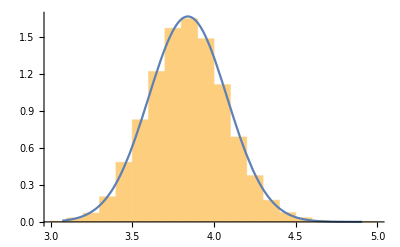

```mathematica
data=Table[ns[n0,T0],10000];
Show[Histogram[data,20,"PDF"],Plot[PDF[NormalDistribution[n0 T0,√n0 T0],x],{x,Min[data],Max[data]}]]
```

```mathematica
Through[{Mean,Variance}[data/256]]
```

{0.0149936,8.85196×10^-7}

```mathematica
√(%⟦2⟧)/%⟦1⟧
```

0.06275

So around the melting temperature, there is a 6.3% standard deviation when generating data.

```mathematica
ClearAll[data];Share[]
```

2279768

### Nelson-Halperin Order Parameter

Ψ=∑_(k≠j) exp i 6 Θ_jk /∑_(k≠j) 1, where the sum is over all particle pairs j and k (and the i in the exponent is the
imaginary unit) and Θjj is the angle of the vector from particle k to particle j with the x axis. Note that the
angle from particle k to j is the compliment of the angle from particle j to k, so we only need to look at
each pair.

```mathematica
θ=Table[n π/3,{n,0,5}]
```

{0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3}

```mathematica
ArcTan[ Cos[θ+ϵ],Sin[θ+ϵ]]
```

{ArcTan[Cos[ϵ],Sin[ϵ]],ArcTan[Sin[π/6-ϵ],Cos[π/6-ϵ]],ArcTan[-Sin[π/6+ϵ],Cos[π/6+ϵ]],ArcTan[-Cos[ϵ],-Sin[ϵ]],ArcTan[-Sin[π/6-ϵ],-Cos[π/6-ϵ]],ArcTan[Sin[π/6+ϵ],-Cos[π/6+ϵ]]}

```mathematica
Exp[I 6 ArcTan[Tan[θ + 0.1]]]
```

{0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ}

```mathematica
Total[%]/6
```

0.825336+0.564642 ⅈ

```mathematica
Abs[%]
```

1.

Where is the point half-way between the nearest neighbors and next nearest neighbors? The next
nearest neighbor to a point at {0, 0} is at {3 a /2, √3 a/2}, a distance of √3 a from {0,0}. The half-way distance between the nearest neighbors at a and the next nearest neighbors at √3 a is (√3-1)a, and adding half that distance to a yields (1+ √3 )a/2.

```mathematica
EuclideanDistance[{0, 0},{3a/2,√3 a/2}]
```

√3 Abs[a]

```mathematica
a79(1+√3)/2
```

2.60177

#### Test Data

Here is some data used to test the Julia MD2 routines.

```mathematica
N[fill[9,9]]
```

<|ρ→0.032075,a→6.,Nr→3.,Nc→3.,Bx→9.,By→7.79423,pn→{{{-7.5,-5.19615},{-1.5,-5.19615},{4.5,-5.19615}},{{-4.5,0.},{1.5,0.},{7.5,0.}},{{-7.5,5.19615},{-1.5,5.19615},{4.5,5.19615}}}|>

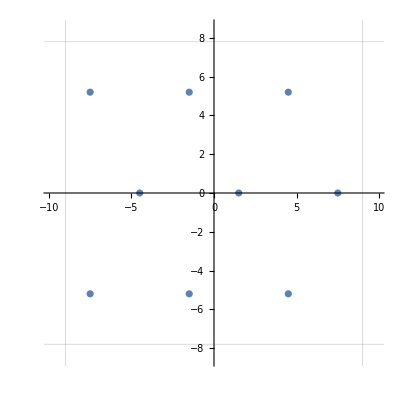

```mathematica
plotPnts[%]
```

#### Potentials 1/r^n

The standard repulsive potential is given by:

```mathematica
ClearAll[rn];
rn[r_, n_]:= 1/r^n
```

Here is the form for a particular n:

```mathematica
rn[r,5]
```

1/r^5

And here are some interesting values of that.

```mathematica
test={1/2, 1, 2,a79, 3, 3.4999, 7/2, 4, nnnd α79, tnnnd};
test::usage="test = {1/2, 1, 2, a79, 3, 3.4999, 7/2, 4, nnnd α79, tnnnd}
	The explicit rationals are good test values whose results are easily done in your head (except for 7/2, which is the skin distance). α79 is the 1/π density as exact number (√(2  π/SqrtBox[3])), a79 as floating point. 3.4999 is just inside the 3.5 skin value. nnnd is the next nearest neighbor distance in a79 units, and tnnnd is the third net nearest neighbor distance (i.e., 2×a79).";
Map[ rn[#,5]&,test]
```

{32,1,1/32,0.0398981,1/243,0.00190424,32/16807,1/1024,1/(12 √2 3^(1/4) π^(5/2)),(3 3^(1/4))/(128 √2 π^(5/2))}

```mathematica
N[%]
```

{32.,1.,0.03125,0.0398981,0.00411523,0.00190424,0.00190397,0.000976563,0.00255946,0.00124681}

```mathematica
N[test]
```

{0.5,1.,2.,1.90463,3.,3.4999,3.5,4.,3.29891,3.80925}

The force is the derivative with respect to r:

```mathematica
f[r_]=D[rn[r,5],r]
```

-5/r^6

Here are the resulting forces at those same interesting values.

```mathematica
Map[f,test]
```

{-320,-5,-5/64,-0.10474,-5/729,-0.00272042,-320/117649,-5/4096,-5/(24 √3 π^3),-(15 √3)/(512 π^3)}

The skin at 3.5σ yields the following ratios to the mean separation in a hexagonal grid:

```mathematica
{rn[3.5,5]/rn[a79,5],f[3.5]/f[a79]}
```

{0.0477208,0.0259687}

The number of particles expected in a circular region of radius r is ρ π r^2, but with the density ρ = 1/π, the expected number of particles is simply r^2

```mathematica
Block[{ρ=1/π},ρ π{3.5^2,5^2}]
```

{12.25,25}

The minimum potential energy of the system on a per particle basis is the energy of six particles at a, and six more at nnnd = √3 a. Therefore the minimum potential energy per particle is half the sum of all twelve (since we ascribe half the potential energy to each pair).

```mathematica
pe=(6rn[a79,5]+6rn[nnnd a79,5])/2
```

0.127373

#### Setting the Potential to Zero at r_skin

The potential has a step in it:

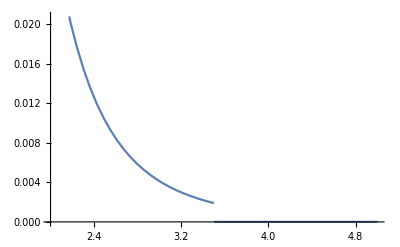

```mathematica
Plot[Piecewise[{{rn[x,5],x<3.5},{0,True}}],{x, 2, 5}]
```

However, the MD2 code has never really dealt with the step, in that the velocity of a particle crossing the step was never diminished in the direction it crossed. In effect, the step was not there, but the potential energy calculation reported it.  If rn[] was defined with the step subtracted, the force would be unchanged, but the potential would be a little lower. The step is at r = 7/2, so the excess P.E. per particle when they are at rest in their minimum P.E. positions is given by:

```mathematica
step=N[12rn[7/2,5]/2]
```

0.0114238

If we were to subtract that from the P.E. function rn[] the per particle P.E would be lower by (in percent):

```mathematica
100step/pe
```

8.96881

At the density of 1/π, the skin radius of 3.5 would have 12.25 particles within the skin. Of course, there are only 12 or 13 particles, never a quarter particle.  On average though there will be 12.25, so when then average per particle increase is

```mathematica
49/4rn[7/2,5]/2
```

4/343

```mathematica
N[%]
```

0.0116618

```mathematica
rn[3.5,5]
```

0.00190397

We can make a three input version of rn[] to account for the skin depth.

```mathematica
ClearAll[rn];
rn::usage="rn[r, n]=r^-n.
rn[r_, n_:5, Rskn_:3.5] respects the skin depth and causes the potential to be zero at the skin depth range.";
rn[r_,n_]:=r^-n;
rn[r_,n_:5,Rskn_:3.5]:=Piecewise[{{0, r≥Rskn}, {rn[r,n]-rn[Rskn,n], True}}]
```

```mathematica
?test
Print[test];Map[rn[#,5,3.5]&, test]
```

test = {1/2, 1, 2, a79, 3, 3.4999, 7/2, 4, nnnd α79, tnnnd}
	The explicit rationals are good test values whose results are easily done in your head (except for 7/2, which is the skin distance). α79 is the 1/π density as exact number (√(2  π/SqrtBox[3])), a79 as floating point. 3.4999 is just inside the 3.5 skin value. nnnd is the next nearest neighbor distance in a79 units, and tnnnd is the third net nearest neighbor distance (i.e., 2×a79).

{1/2,1,2,1.90463,3,3.4999,7/2,4,3^(1/4) √(2 π),(2 √(2 π))/3^(1/4)}

{31.9981,0.998096,0.029346,0.0379941,0.00221126,2.72019×10^-7,0,0,0.000655494,0}

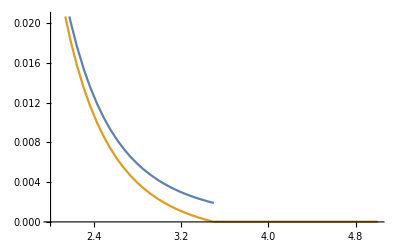

```mathematica
Plot[{Piecewise[{{rn[x,5],x<3.5},{0,True}}],rn[x,5,3.5]},{x, 2, 5}]
```

We can find the nearest points in the following way. Note that when the points are left in symbolic form, the distance returned is the square for some unknown reason, so we apply N[] to pnts256.

```mathematica
Nearest[Flatten[N[pnts256⟦"pn"⟧],1]-> All,N[p2],{All,3.5}]
```

{<|Element→{10.9516,5.77309},Index→190,Distance→0.|>,<|Element→{9.99928,7.42254},Index→206,Distance→1.90463|>,<|Element→{11.9039,7.42254},Index→207,Distance→1.90463|>,<|Element→{12.8562,5.77309},Index→191,Distance→1.90463|>,<|Element→{9.99928,4.12364},Index→174,Distance→1.90463|>,<|Element→{9.04697,5.77309},Index→189,Distance→1.90463|>,<|Element→{11.9039,4.12364},Index→175,Distance→1.90463|>,<|Element→{10.9516,9.072},Index→222,Distance→3.29891|>,<|Element→{8.09466,7.42254},Index→205,Distance→3.29891|>,<|Element→{13.8085,7.42254},Index→208,Distance→3.29891|>,<|Element→{8.09466,4.12364},Index→173,Distance→3.29891|>,<|Element→{13.8085,4.12364},Index→176,Distance→3.29891|>,<|Element→{10.9516,2.47418},Index→158,Distance→3.29891|>}

This includes the zero distance to p2.  We need to remove p2 from the particle list.  p2 is particle 190, and we can remove it as follows:

```mathematica
Nearest[Delete[Flatten[N[pnts256⟦"pn"⟧],1],190]-> All,N[p2],{All,3.5}]
```

{<|Element→{9.99928,7.42254},Index→205,Distance→1.90463|>,<|Element→{11.9039,7.42254},Index→206,Distance→1.90463|>,<|Element→{12.8562,5.77309},Index→190,Distance→1.90463|>,<|Element→{9.99928,4.12364},Index→174,Distance→1.90463|>,<|Element→{9.04697,5.77309},Index→189,Distance→1.90463|>,<|Element→{11.9039,4.12364},Index→175,Distance→1.90463|>,<|Element→{10.9516,9.072},Index→221,Distance→3.29891|>,<|Element→{8.09466,7.42254},Index→204,Distance→3.29891|>,<|Element→{13.8085,7.42254},Index→207,Distance→3.29891|>,<|Element→{8.09466,4.12364},Index→173,Distance→3.29891|>,<|Element→{13.8085,4.12364},Index→176,Distance→3.29891|>,<|Element→{10.9516,2.47418},Index→158,Distance→3.29891|>}

Rather than work with a list of associations, we can simply ask for the distances.

```mathematica
skinlst =Nearest[Delete[Flatten[N[pnts256⟦"pn"⟧],1],190]-> "Distance",N[p2],{All,3.5}]
```

{1.90463,1.90463,1.90463,1.90463,1.90463,1.90463,3.29891,3.29891,3.29891,3.29891,3.29891,3.29891}

These can be handed to rn[] to compute the PEs as a list:

```mathematica
rn[skinlst,5]/2
```

{0.019949,0.019949,0.019949,0.019949,0.019949,0.019949,0.00127973,0.00127973,0.00127973,0.00127973,0.00127973,0.00127973}

Summing is easy:

```mathematica
pe12=Apply[Plus,%]
```

0.127373

The result is lower for the version corrected for the PE step (and this is a test value for the Julia code).

```mathematica
NumberForm[pe12o=Apply[Plus,Map[rn[#,5, 7/2]/2&,skinlst]], {11,10}]
```

0.1159487884

```mathematica
NumberForm[pe12o,{11,10}]
```

0.1159487884

```mathematica
pe12-pe12o
```

0.0114238

#### Potential Function in the Field of Particles

We would like to know how the potential energy of a particle will vary as it move directly toward another particle.  We know that there are particles just outside the skin, so we must account for them by recomputing the distance to all particles as we move.

```mathematica
ClearAll[Pdx];
Pdx::usage="Pdx[p_Integer,pnts_Association,Rskn_,n_5] returns a function of {x,y} which computes the 
potential energy of particle number p moved a distance of {x, y} from its home (crystaline) position 
based on all the other particles being in thier home positions with a potential function of 1/r^n and a 
range of Rskn. The function does not enforce periodic boundary conditions.";
Pdx[p_Integer,pnts_Association,Rskn_,n_:5]:= 
	Module[{pntarry=Flatten[N[pnts⟦"pn"⟧],1],point},
		point=N[pntarry⟦p⟧];
		Function[{x,y},
			Module[{dev=point+{x,y},skinlst},
			skinlst=Nearest[Delete[pntarry,p]-> "Distance",dev,{All,Rskn}];
			(*Print[skinlst];*)
			Apply[Plus, rn[#,n,Rskn]/2& /@ skinlst]]]]
```

This creates the function for particle 190:

```mathematica
P256=Pdx[190,pnts256,Rskin]
```

Function[{x$,y$},Module[{dev$=point$12713+{x$,y$},skinlst$},skinlst$=Nearest[Delete[pntarry$12713,190]→Distance,dev$,{All,3.5}];Plus@@(1/2 rn[#1,5,3.5]&)/@skinlst$]]

Here is its use.

```mathematica
P256[3a79/2,0]
```

1.36316

We will want to mark a few particular distances, and we’ll define a function to help do that.

```mathematica
ClearAll[Vline];
Vline::usage="Vlin[x] can be used to draw a vertical line at x in a plot.  Suggested use is 
Prolog→{Directive[Gray,Dashed],Vline[x1],Vline[x2]} inside a Plot[] function call."
Vline[x_]:=Line[{Scaled[{0,-1},{x,0}], Scaled[{0,1},{x,0}]}]
```

Vlin[x] can be used to draw a vertical line at x in a plot.  Suggested use is 
Prolog→{Directive[Gray,Dashed],Vline[x1],Vline[x2]} inside a Plot[] function call.

The plot below shows the challenge.  While moving along the x-axis, we are moving directly toward the next particle and the energy quickly diverges, starting to grow rapidly once it gets half way.  On the other hand, as it moves along the y-axis, the potential follows an r^-2profile, oscillates a bit as it slips between adjacent particles, and then starts diverging as it approaches the particle two rows above.

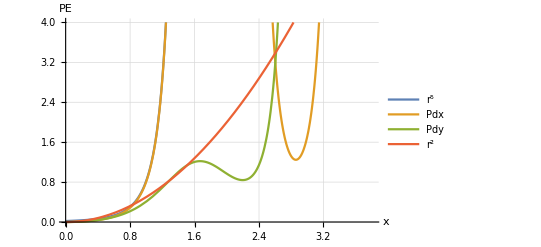

```mathematica
Plot[{rn[a79-x,5]/2,P256[x,0]-pe12o,P256[0,x]-pe12o,x^2/2},{x, 0, 2a79},
	PlotLegends->{"r^5","Pdx","Pdy","r^2"},GridLines->Automatic,
	PlotRange->{{0, 2a79},{0, 4}},AxesLabel->{x,"PE"},
	Prolog->{Directive[Gray,Dashed],Vline[a79/2],Vline[a79],Vline[3a79/2]}]
```

The contour plot below shows the energy (clipped to a maximum value of 2) around the center of particle 190.  The six large red circles are more-or-less centered on the adjacent particles

```mathematica
ContourPlot[Clip[P256[x,y],{0,2}],{x,-#,#},{y,-#,#},Contours->30,ColorFunction->Hue,PlotLegends->Automatic]&[a79]
```

-Graphics-

A 3-D plot shows the valley clearly.

```mathematica
Plot3D[Clip[P256[x,y],{0,2}],{x,-#,#},{y,-#,#},ColorFunction->Hue,PlotLegends->Automatic]&[a79]
```

-Graphics3D-

So there is a broad, flat valley in which the particles move mostly freely with narrow passes that higher energy particles may approach. If we take the melting point to be at T = 0.01283, which is also the per particle kinetic energy, it is reasonable to assume that the same mean energy would find its way into potential energy.  Below we show the expected mean PE for both the transition temperature and the high fluid temp of T = 0.02, and at three times that high temperature.

```mathematica
pe12o + {0.01283, 0.02, 3*0.02}
```

{0.128779,0.135949,0.175949}

We need to zoom into the contour plot to see what the potential looks like down there.  The plot below shows that the contours are basically circular out to at least PE = 0.19.  The mean PE then can be achieved by using a circular Gaussian distribution whose standard deviation is the mean PE corresponding to the desired temperature.  We should be concerned that extreme deviations (3σ) might extend into the less circular regions of the potential, but again the plot below shows that it does not.

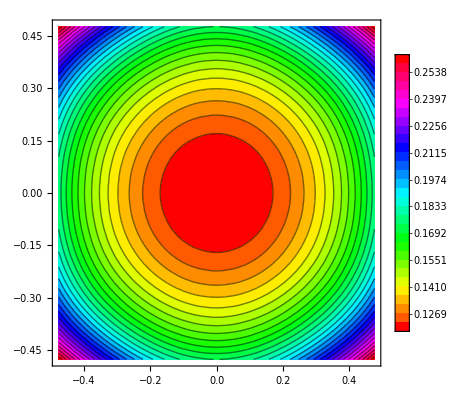

```mathematica
zcp=ContourPlot[Clip[P256[x,y],{0,2}],{x,-#,#},{y,-#,#},Contours->30,ColorFunction->Hue,PlotLegends->Automatic]&[a79/4]
```

```mathematica
Export["zcp.pdf",zcp]
```

zcp.pdf

Below is a look at the shape of a few versions of models we might use. We see the justification for the calling the PE field circular, as the Pdx and Pdy plots are nearly identical of the range of interest.  r^-2/4 does not fit very well, and the function which is the potential between two particles spaced a 2a (rn2[], defined below) appears slightly slow.  We will now plot only the excess energy.

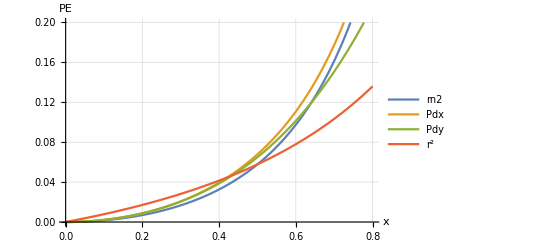

```mathematica
rn2[x_,a_,n_]:=(rn[a-x,n]-2rn[a,n]+rn[a+x,n])/2
rna79=rn[a79,5];
pz2=Plot[{rn2[x,a79,5],P256[x,0]-pe12o,P256[0,x]-pe12o,((a79-x)^-2-a79^-2)/4},{x, 0,0.8},PlotLegends->{"rn2","Pdx","Pdy","r^2"},GridLines->Automatic,AxesLabel->{x,"PE"},PlotRange->{{0, 0.8},{0, 0.2}}]
```

```mathematica
Export["pz2.pdf",pz2]
```

pz2.pdf

We’ll make a table of values between Pdx and Pdy.

```mathematica
tabP256=Table[{x,((P256[x,0]+P256[0,x]))/2-pe12o},{x,0,0.55,0.001}];
tabP256⟦1;;10⟧
```

{{0.,0.},{0.001,2.10631×10^-7},{0.002,8.42528×10^-7},{0.003,1.89569×10^-6},{0.004,3.37014×10^-6},{0.005,5.26589×10^-6},{0.006,7.58295×10^-6},{0.007,0.0000103213},{0.008,0.0000134811},{0.009,0.0000170623}}

```mathematica
fit=FindFormula[tabP256,x,6, RandomSeeding->4]
```

{0.218418 x^2.-0.518022 x^3.+12.628 x^4.+1014.38 x^6.-4155.3 x^7.+10473.1 x^8.-15898.7 x^9.+13339.3 x^10.-4752.92 x^11.-149.231 Abs[x]^5.,0.218262 x^2.-0.511177 x^3.+12.5051 x^4.+1007.48 x^6.-4130.17 x^7.+10415.1 x^8.-15816.4 x^9.+13273.6 x^10.-4730.44 x^11.-148.042 Abs[x]^5.,0.219394 x^2.-0.556786 x^3.+13.2753 x^4.+1047.27 x^6.-4270.97 x^7.+10732.5 x^8.-16258.1 x^9.+13619.8 x^10.-4847.3 x^11.-155.154 Abs[x]^5.,0.217825 x^2.-0.493556 x^3.+12.2081 x^4.+992.243 x^6.-4076.43 x^7.+10294.4 x^8.-15649. x^9.+13142.9 x^10.-4686.45 x^11.-145.308 Abs[x]^5.,0.219694 x^2.-0.568898 x^3.+13.4795 x^4.+1057.75 x^6.-4307.96 x^7.+10815.6 x^8.-16373.4 x^9.+13709.9 x^10.-4877.61 x^11.-157.034 Abs[x]^5.,0.217574 x^2.-0.484186 x^3.+12.0598 x^4.+985.356 x^6.-4053.11 x^7.+10243.9 x^8.-15581.1 x^9.+13091.4 x^10.-4669.58 x^11.-144.014 Abs[x]^5.}

FindFormula[] uses some randomization, and it can be difficult to repeat results.  One very hopeful result on some prior work was a simple a+b x Tan[x], but I lost the parameters.  I added another parameter and used FindFit[] to get estimates of the parameters. In practice, the a parameter was small and negative, which give the analog a negative value for small energies, and this is of course where the function will live.  Therefor, we fit b x Tan[c x].

```mathematica
fit2=FindFit[tabP256,b x Tan[c x], {b,c},x]
```

{b→0.14406,c→1.48849}

```mathematica
ScientificForm[{b, c} //. fit2, 15]
```

{1.44060465027302×10^-1,1.48849049313253}

That last equation is reasonably simple. We can also fit rn2[a x].

```mathematica
fit3=FindFit[tabP256, rn2[a x,a79,5],{a},x]
```

{a→1.05616}

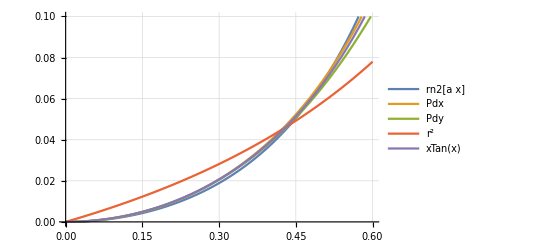

```mathematica
rna79=rn[a79,5];
(* xTx1[x]:=0.2502535780455324 x Tan[x];*)
xTx2[x_]=b x Tan[c x]//.fit2;
Plot[{rn2[1.05616x,a79,5],P256[x,0]-pe12o,P256[0,x]-pe12o,((a79-x)^-2-a79^-2)/4, xTx2[x]},{x, 0,0.6},PlotLegends->{"rn2[a x]","Pdx","Pdy","r^2","xTan(x)"},GridLines->Automatic,PlotRange->{{0, 0.6},{0, 0.1}}]
```

The difficulty with the xTanx function is that it is very specific to the density and exponent.

The mean excess PE will be equal to the mean temperature, and the highest we are interested in simulating is around T = 0.02. The distance from the minimum PE will be given by the solution to the following:

```mathematica
ScientificForm[FindRoot[xTx2[x]==0.2,{x,0.3}],15]
```

{x→7.30052667340978×10^-1}

{x→7.30052667340978×10^-1}

{x→7.30052667340978×10^-1}

«3 more identical outputs»

FindRoot[] won’t work with the way Pdx[] is defined, but we can easily find it by hand.

```mathematica
{P256[0.2955,0]-(pe12o+0.02),P256[0,0.2964]-(pe12o+0.02),P256[0.294917,0]-(pe12o+0.02)}
```

{7.30325×10^-6,8.19287×10^-7,-0.00007853}

#### Initializing with Gaussian Deviations

Let’s generate 256 random points in the plane.

```mathematica
dev=RandomVariate[NormalDistribution[0,0.2955],{256,2}];
```

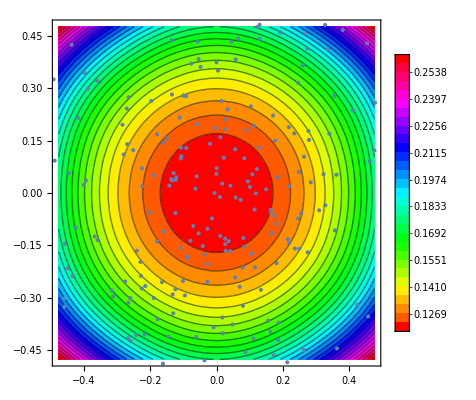

```mathematica
Show[zcp,ListPlot[dev]]
```

Find the point farthest from the center.

```mathematica
Max@@Apply[Sqrt[#1^2+#2^2]&,dev,2]
```

0.948652

Check that PE in the x, y, and diagonal direction. They are all different, as they are well outside the “circular” region.

```mathematica
{P256[#,0],P256[0,#],P256[#/√2,#/√2]}&[%]
```

{0.724909,0.466806,0.586883}

Compute the PE at each point.

```mathematica
pedev=Apply[P256,dev,2];
pedev⟦1;;10⟧
```

{0.221293,0.118891,0.162902,0.120518,0.119512,0.125137,0.138512,0.11816,0.132577,0.123146}

The max PE is large.

```mathematica
Max@@pedev
```

0.689319

However, the mean is below what we hoped for.  This is due to the wide flat bottom of the potential well.

```mathematica
{Mean[#],StandardDeviation[#]}&[pedev]
```

{0.17278,0.081513}

#### Using the Boltzmann Distribution to Initialize

Simply using a Gaussian  was hoped to achieve a good-enough distribution of particles that was not starting in the odd state of passing through the minimum PE state. We turn now to the Boltzman distribution, which states that the energy will be an exponential distribution P(E) = e^(-E/β), where β is 1/T (in scaled units).  The PE is roughly circular out to about a total PE of 0.2.  The E here is the excess PE above the minimum PE.

```mathematica
0.2-pe12o
```

0.0840512

Here is a picture of that distribution for T = 0.02.

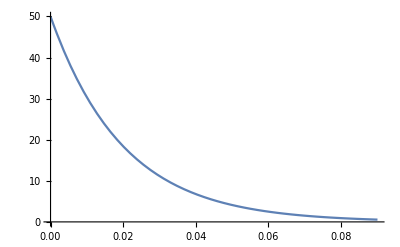

```mathematica
Plot[PDF[ExponentialDistribution[1/0.02],x],{x,0,.09}]
```

For each particle, we generate a potential energy E_0 increase from the exponential distribution, generate a random direction, and then place the particle along that direction such that its excess PE matches E_0. We would like an inverse function for that.

```mathematica
InverseFunction[xTx2[x]]
```

InverseFunction[0.14406 x Tan[1.48849 x]]

That was useless.  We can use FinddRoot[] to perform the inverse for us.

```mathematica
NumberForm[FindRoot[xTx2[x]==0.2,{x,.3}], 15]
```

{x→0.730052667340978}

```mathematica
xTx2[x]-0.2/.%
```

8.32667×10^-17

We can try to make a series and invert that.  Here is a sixth order series for xTx[]:

```mathematica
ClearAll[sxTx6];
sxTx6[x_]:=Evaluate[Normal[Series[xTx2[x],{x,0,6}]]]
```

Here, we plot its error.

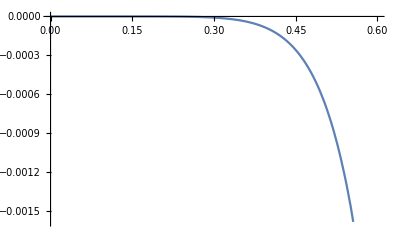

```mathematica
Plot[sxTx6[x]-xTx2[x],{x,0,0.6}]
```

And here is yet another fruitless attempt to invert it.

```mathematica
InverseSeries[sxTx6]
```

InverseSeries[sxTx6]

We can also find a formula for the inverse curve.  The very large coefficients mean it is a poor formula.

```mathematica
invfit=FindFormula[Table[{P256[x,0],x},{x,0,0.55,0.001}],x]
```

-3475.82+154825. x-2.94203×10^6 x^2.+3.09105×10^7 x^3.-1.93903×10^8 x^4.+7.26217×10^8 x^5.-1.50358×10^9 x^6.+1.32763×10^9 x^7.

We’ll start by generating 256 samples of an exponential distribution.

```mathematica
e256=RandomVariate[ExponentialDistribution[1/0.02],256];
e256⟦1;;10⟧
```

{0.0136874,0.00299511,0.000700403,0.00503369,0.01354,0.0238061,0.0046755,0.00255982,0.0407606,0.0137259}

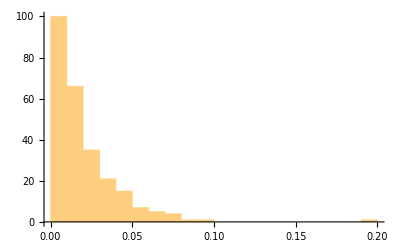

```mathematica
Histogram[e256]
```

This next expression will map them through FindRoot[] to the xTx2[] input which would have caused them.

```mathematica
r=Map[x/.FindRoot[xTx2[x]==#,{x,0.3}]& ,e256];
r⟦1;;10⟧
```

{0.246844,0.117579,0.0570828,0.151898,0.245573,0.320134,0.146483,0.10878,0.407634,0.247175}

The histogram of that result looks more Normal than Exponential.

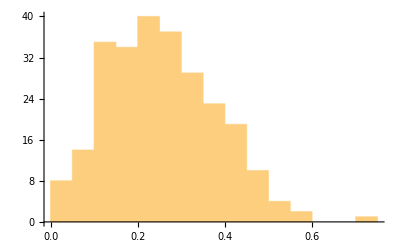

```mathematica
Histogram[r]
```

Mapping back through xTx2[] returns our exponential result.

```mathematica
Histogram[xTx2[r]]
```

-Graphics-

Now we generate 256 angles between zero and 2π.

```mathematica
angles=RandomVariate[UniformDistribution[{0,2π}],256];
angles⟦1;;10⟧
```

{3.19211,3.84044,0.494163,2.37532,4.87944,5.13643,0.60591,0.798764,2.30174,0.143429}

The expression below will will take each deviation and angle and form an {x,y} pair.

```mathematica
dev2=Thread[{#1Cos[#2],#1Sin[#2]}&[r,angles]];
dev2⟦1;;10⟧
```

{{-0.246529,-0.0124644},{-0.0900165,-0.0756423},{0.0502538,0.0270741},{-0.109442,0.105335},{0.0408337,-0.242154},{0.131719,-0.291781},{0.120407,0.0834239},{0.0758843,0.0779404},{-0.272124,0.303502},{0.244637,0.0353306}}

We can see below that the samples are more concentrated in the center than the Gaussian one was.

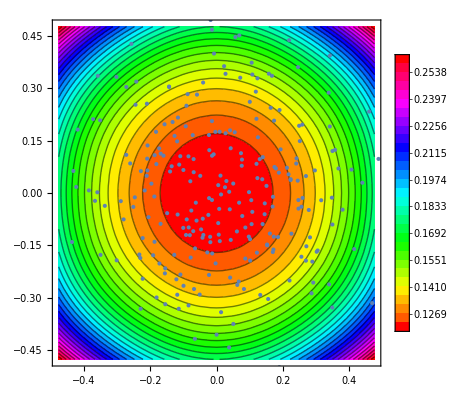

```mathematica
Show[zcp,ListPlot[dev2]]
```

Find the point farthest from the center. This is smaller than the previous result, which is often greater than one.

```mathematica
Max@@Apply[Sqrt[#1^2+#2^2]&,dev2,2]
```

0.721083

Check that PE in the x, the y, and the diagonal direction. They are all similar, as they are well inside the “circular” region.

```mathematica
{P256[#,0],P256[0,#],P256[#/√2,#/√2]}&[%]
```

{0.311859,0.279036,0.295255}

Compute the PE at each point.

```mathematica
pedev2=Apply[P256,dev2,2];
pedev2⟦1;;10⟧
```

{0.129515,0.118894,0.116637,0.120903,0.129358,0.139783,0.12055,0.118466,0.156947,0.129548}

The max PE is reasonable.

```mathematica
Max@@pedev2
```

0.288974

The mean is about what we hoped for.

```mathematica
{Mean[#],StandardDeviation[#]}&[pedev2]
```

{0.13562,0.0202939}

The mean is only a bit higher than our target.

```mathematica
pe12o+0.02
```

0.135949

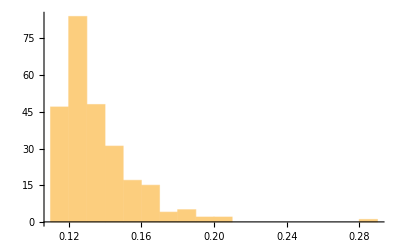

```mathematica
Histogram[pedev2]
```

In Julia, the root can be found with the Roots.jl package (note: xTx2 changed from this snapshot):

julia> xTx(x) = 0.138006 * x * tan(1.55419 * x)

julia> f(x,p) = xTx(x) - p
f (generic function with 2 methods)

julia> find_zero( f, 0.3, 0.02)
0.2949171886685355

```mathematica
Share[]
```

4206352

### Distribution of Regressions of Uncorrelated Data

The difficulty of deciding when the temperature profiles are truly uncorrelated requires we examine the distribution of the slope estimate.

```mathematica
βe = (∑_(i=1)^n Subscript[x, i] Subscript[y, i]-n x̄ ȳ)/((n-1)Sx^2)
```

(-n x̄ ȳ+∑_(i=1)^n x_i y_i)/((-1+n) Sx^2)

where S_x^2 is the variance of the x_i.  In our case, x_i is simply the series 1:n., so we can replace x̄ and S_x^2 with exact values (and we use the actual variance, not the sample variance, of x; Mathematica needs to know that these numbers are the full population or it will return the sample variance):

```mathematica
Variance[DiscreteUniformDistribution[{1, n}]]
```

1/12 (-1+n^2)

```mathematica
Simplify[{1/n∑_(i=1)^n i,∑_(i=1)^n i^2,1/n∑_(i=1)^n (i-(n+1)/2)^2},Assumptions-> n>3]
```

{(1+n)/2,1/6 n (1+n) (1+2 n),1/12 (-1+n^2)}

```mathematica
βe2=Simplify[βe//.{Subscript[x, i]-> i,Sx->√((n^2-1)/12),x̄-> (n+1)/2, ȳ-> 1/n∑_(i=1)^n Subscript[y, i]},Assumptions-> n>3]
```

(-6 (1+n) ∑_(i=1)^n y_i+12 ∑_(i=1)^n i y_i)/((-1+n)^2 (1+n))

We can combine the two sums in the numerator:

```mathematica
βe3=FullSimplify[(12 ∑_(i=1)^n Subscript[y, i](i-(n+1)/2))/((-1+n)^2 (1+n)),Assumptions-> n>3]
```

(12 ∑_(i=1)^n (i+1/2 (-1-n)) y_i)/((-1+n)^2 (1+n))

The coefficients of the y_i will sum to be the multiplier of the mean of y (which is the average temperature), sums to zero (so the slope doesn’t depend on the average temperature).

```mathematica
FullSimplify[∑_(i=1)^n (i-(n+1)/2) ]
```

0

The sum of the squares of the coefficient is the multiplier of the variance of y.

```mathematica
FullSimplify[∑_(i=1)^n (i-(n+1)/2)^2 ]
```

1/12 n (-1+n^2)

Combining everything together, the overall multiplier must be squared, which will divide the factor of twelve out:

```mathematica
n2[n_]=FullSimplify[(12/((-1+n)^2 (1+n)))^2 1/12 n (-1+n^2),Assumptions->n>3]
```

(12 n)/((-1+n)^3 (1+n))

That function goes down as n^-3, and the standard deviation as the square root of that.

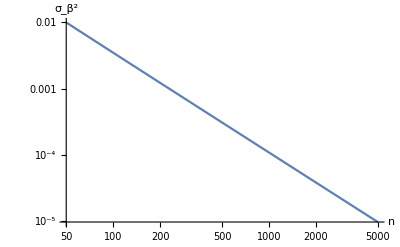

```mathematica
LogLogPlot[√n2[n],{n,50,5000},PlotRange->Full,GridLines->Automatic,AxesLabel-> {"n", Subscript[σ, β]^2}]
```

The relative error of the n^-3 approximation is below, going from 4% at n = 50, to less than 0.04% at 5,000:

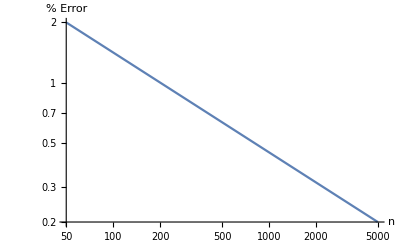

```mathematica
LogLogPlot[√(100(Abs[12 n^-3-n2[n]])/n2[n]),{n,50,5000},PlotRange->Full,GridLines->Automatic,AxesLabel-> {"n","% Error"}]
```

```mathematica
√(100Abs[12 n^-3-n2[n]]/n2[n])//. n-> 5000
```

(√249999990001)/2500000

```mathematica
N[%]
```

0.2

#### Relationship Between t_r and F

There appears to be an algebraic relationship between the t statistic for the regression ratio (t_r) and the F statistic.

```mathematica
ClearAll[S,y,ν,α,β,i,n]
```

```mathematica
F1=(Subscript[ν, 2](∑_(i=1)^n (Subscript[y, i]-ȳ)^2-∑_(i=1)^n (Subscript[y, i]-Subscript[ŷ, i])^2))/(Subscript[ν, 1]∑_(i=1)^n (Subscript[y, i]-Subscript[ŷ, i])^2)
```

(ν_2 (∑_(i=1)^n (-ȳ+y_i)^2-∑_(i=1)^n (y_i-(ŷ)_i)^2))/(ν_1 ∑_(i=1)^n (y_i-(ŷ)_i)^2)

```mathematica
ExpandAll[F1]
```

-ν_2/ν_1+(ν_2 ∑_(i=1)^n (-ȳ+y_i)^2)/(ν_1 ∑_(i=1)^n (y_i-(ŷ)_i)^2)

```mathematica
rules={∑_(i_=1)^n a_:>a n/;FreeQ[a,i],∑_(i_=1)^n a_ b_.:>a ∑_(i=1)^n b/;FreeQ[a,i], ∑_(i_=1)^n a_^2:> ∑_(i=1)^n Expand[a^2], ∑_(i_=1)^n a_-∑_(i_=1)^n b_.:> ∑_(i=1)^n FullSimplify[a-b, Assumptions-> i>3],∑_(i_=1)^n (a_+b_):> ∑_(i=1)^n a+∑_(i=1)^n b,∑_(i_=1)^n Subscript[y, i]:>n ȳ,Subscript[ŷ, i_]^2-> ( α+β i)^2,Subscript[ŷ, i]->  α+β i,∑_(i=1)^n Subscript[y, i]^2 - n (ȳ)^2-> n Subscript[S, y]^2}
```

{∑_(i_=1)^n a_:>a n/;FreeQ[a,i],∑_(i_=1)^n a_ b_.:>a ∑_(i=1)^n b/;FreeQ[a,i],∑_(i_=1)^n a_^2:>∑_(i=1)^n Expand[a^2],-∑_(i_=1)^n b_.+∑_(i_=1)^n a_:>∑_(i=1)^n FullSimplify[a-b,Assumptions→i>3],∑_(i_=1)^n (a_+b_):>∑_(i=1)^n a+∑_(i=1)^n b,∑_(i_=1)^n y_i:>n ȳ,(ŷ)_i_^2→(α+i β)^2,(ŷ)_i→α+i β,-n (ȳ)^2+∑_(i=1)^n y_i^2→n S_y^2}

```mathematica
F2=ExpandAll[F1]//. rules
```

-ν_2/ν_1+(n S_y^2 ν_2)/(ν_1 (-2 ∑_(i=1)^n (α+i β) y_i+∑_(i=1)^n y_i^2+∑_(i=1)^n (ŷ)_i^2))

```mathematica
F3=-Subscript[ν, 2]/Subscript[ν, 1]+(n Subscript[S, y]^2 Subscript[ν, 2])/(Subscript[ν, 1] (-2 ∑_(i=1)^n (Subscript[αy, i]+i Subscript[βy, i])+∑_(i=1)^n Subscript[y, i]^2+∑_(i=1)^n ( α+β i)^2))//.rules
```

-ν_2/ν_1+(n S_y^2 ν_2)/(ν_1 (1/6 (6 n α^2+6 n α β+6 n^2 α β+n β^2+3 n^2 β^2+2 n^3 β^2)+∑_(i=1)^n y_i^2-2 (∑_(i=1)^n αy_i+∑_(i=1)^n i βy_i)))

```mathematica
FullSimplify[%]
```

(ν_2 (-1+(n S_y^2)/(n α^2+n (1+n) α β+1/6 n (1+n) (1+2 n) β^2+∑_(i=1)^n y_i^2-2 (∑_(i=1)^n αy_i+∑_(i=1)^n i βy_i))))/ν_1

We can combine the sums, and convince Mathematica to get to a form useful in sums.

```mathematica
F2=(Subscript[ν, 2]∑_(i=1)^n (Expand[FullSimplify[(Subscript[y, i]-ȳ)^2-(Subscript[y, i]-Subscript[ŷ, i])^2]]))/(Subscript[ν, 1]∑_(i=1)^n (Subscript[y, i]-Subscript[ŷ, i])^2)
```

(ν_2 ∑_(i=1)^n ((ȳ)^2-2 ȳ y_i+2 y_i (ŷ)_i-(ŷ)_i^2))/(ν_1 ∑_(i=1)^n (y_i-(ŷ)_i)^2)

Now we need to distribute the sums, and realize that ∑_(i=1)^n y_i=n ȳ and that (ŷ)_i=α̂+β̂ i (where we implicitly make x_i=i)

```mathematica
F3=(Subscript[ν, 2](n (ȳ)^2-2n (ȳ)^2+∑_(i=1)^n (2 Subscript[y, i] Subscript[ŷ, i]-Subscript[ŷ, i]^2)))/(Subscript[ν, 1] ∑_(i=1)^n (Subscript[y, i]-Subscript[ŷ, i])^2)//.Subscript[ŷ, i]-> α+β i
```

(ν_2 (-n (ȳ)^2+∑_(i=1)^n (-(α+i β)^2+2 (α+i β) y_i)))/(ν_1 ∑_(i=1)^n (-α-i β+y_i)^2)

```mathematica
F4=(Subscript[ν, 2] (-n (ȳ)^2+∑_(i=1)^n Expand[FullSimplify[(-(α+i β)^2+2 (α+i β) Subscript[y, i])]]))/(Subscript[ν, 1] ∑_(i=1)^n (-α-i β+Subscript[y, i])^2)
```

(ν_2 (-n (ȳ)^2+∑_(i=1)^n (-α^2-2 i α β-i^2 β^2+2 α y_i+2 i β y_i)))/(ν_1 ∑_(i=1)^n (-α-i β+y_i)^2)

```mathematica
F5=(Subscript[ν, 2] FullSimplify[(-n (ȳ)^2-n α^2-2 α β(n(n+1)/2)-β^2 1/6 n (1+n) (1+2 n)+2α∑_(i=1)^n Subscript[y, i]+2β∑_(i=1)^n i Subscript[y, i])])/(Subscript[ν, 1] (∑_(i=1)^n Expand[(-α-i β+Subscript[y, i])^2]))
```

(ν_2 (-n α^2-n (1+n) α β-1/6 n (1+n) (1+2 n) β^2-n (ȳ)^2+2 α ∑_(i=1)^n y_i+2 β ∑_(i=1)^n i y_i))/(ν_1 ∑_(i=1)^n (α^2+2 i α β+i^2 β^2-2 α y_i-2 i β y_i+y_i^2))

## Velocity Distribution

The temperature is defined by  ⟨E⟩ = 1/2 m ⟨v_x^2⟩+1/2 m ⟨v_y^2⟩=k_b T.  In our units, m and k_b are one.  The other useful fact is that the velocities are Gaussian distributed with zero mean and

## Isobar and Isotherm

```mathematica
Solve[ρ1 T1^(2/n)==ρ2 T2^(2/n)&&P1/(ρ1 T1)==P2/(ρ2 T2)&&n>=1, {ρ2, T2}, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[T1^(2/n) ρ1==T2^(2/n) ρ2&&P1/(T1 ρ1)==P2/(T2 ρ2)&&n≥1,{ρ2,T2},ℝ]

We know n, so plug in 5.

```mathematica
Solve[ρ1 T1^(2/5)==ρ2 T2^(2/5)&&P1/(ρ1 T1)==P2/(ρ2 T2), {ρ2, T2}, Reals]
```

{{ρ2→ConditionalExpression[(T1^(2/5) ρ1)/(Root[-P2^5 T1^3+P1^5 #1^3&,1]^(2/5)),(P1>0&&P2>0&&T1>0)||(P1<0&&P2<0&&T1>0)],T2→ConditionalExpression[Root[-P2^5 T1^3+P1^5 #1^3&,1],(P1>0&&P2>0&&T1>0)||(P1<0&&P2<0&&T1>0)]}}

^2

That looked like it worked, but the Root expression is not simple to work with.  Let’s try a list of equations.

```mathematica
Solve[{ρ1 T1^(2/n)==ρ2 T2^(2/n),P1/(ρ1 T1)==P2/(ρ2 T2),n≥1}, {ρ2, T2}, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{T1^(2/n) ρ1==T2^(2/n) ρ2,P1/(T1 ρ1)==P2/(T2 ρ2),n≥1},{ρ2,T2},ℝ]

How about Reduce.

```mathematica
Reduce[{ρ1 T1^(2/n)==ρ2 T2^(2/n),P1/(ρ1 T1)==P2/(ρ2 T2),n≥1}, {ρ2, T2}, Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{T1^(2/n) ρ1==T2^(2/n) ρ2,P1/(T1 ρ1)==P2/(T2 ρ2),n≥1},{ρ2,T2},ℝ]

Again, let’s plug in 5 for n, and add constraints on T1, P1, P2, & ρ1.

```mathematica
Reduce[{ρ1 T1^(2/5)==ρ2 T2^(2/5),P1/(ρ1 T1)==P2/(ρ2 T2),n≥1,P1>0,T1>0, ρ1>0,P2>0},{ρ2,T2},Reals]
```

n≥1&&ρ1>0&&T1>0&&P2>0&&P1>0&&ρ2==Root[-P1^2 ρ1^3+P2^2 #1^3&,1]&&T2==(P2 T1 ρ1)/(P1 ρ2)

So T2 gives us the expected result.  The new density though is the root of a third order polynomial

```mathematica
-P1^2 ρ1^3+P2^2 #1^3&[x]
```

P2^2 x^3-P1^2 ρ1^3

## Application of the Virial Theorem

The Virial Theorem for r^-n potentials states that the total kinetic energy is related to the total potential energy as 2⟨K_T⟩=-n⟨U_T⟩, where the angle brackets denote averages. Combine this with the pressure equation P = ρ⟨K_T⟩(1+(n⟨U_T⟩)/(2⟨K_T⟩)), where ρ is the density, the pressure becomes simply 2ρ⟨K_T⟩

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Sun 1 Oct 2023. Please